```mathematica
ClearAll["`*"]
SetDirectory[NotebookDirectory[]];
eqs=<<eqs.m;
eqsz0=<<eqsz0.m;
eqsz1=<<eqsz1.m;
eqsxb=<<eqsxb.m;
jacobi=<<jacobi.m;
jacobiz0=<<jacobiz0.m;
jacobiz1=<<jacobiz1.m;
jacobixb=<<jacobixb.m;
eqs//MatrixForm(*运动方程*)
jacobi//MatrixForm(*Jacobi*)
```

(Q6[z,x] (-z+Q7[z,x]^2/(1-z^3))+Q6^(0,2)[z,x]-3 z^2 Q6^(1,0)[z,x]+(1-z^3) Q6^(2,0)[z,x]
-Q6[z,x]^2 Q7[z,x]+Q7^(0,2)[z,x]+(1-z^3) Q7^(2,0)[z,x])

(eye (-z-Q7[z,x]^2/(-1+z^3))+d_(0,2)-3 z^2 d_(1,0)+(1-z^3) d_(2,0) | -(2 eye Q6[z,x] Q7[z,x])/(-1+z^3)
-2 eye Q6[z,x] Q7[z,x] | -eye Q6[z,x]^2+d_(0,2)+(1-z^3) d_(2,0))

```mathematica
mu=5.6;Lz=1;Lx=20.0;cuttoff=1.-10.^-9;
Nz=30;Nx=60;Nzx=Nz*Nx;(*采点数*)
speye=IdentityMatrix[Nzx]//SparseArray;spzero=ConstantArray[0.,{Nzx,Nzx}]//SparseArray;
cgl[n_]:=Table[Cos[(i π)/(n-1.0)],{i,n-1,0,-1}];(*格点*)
gridz=0.5(cgl[Nz]+1);
gridx=0.5Lx cgl[Nx];
zz=gridz⊗ConstantArray[1,Nx];Z=Flatten[zz];
xx=ConstantArray[1,Nz]⊗gridx;X=Flatten[xx];
z0=Flatten[Position[Z,n_/;n==gridz⟦1⟧]];
z1=Flatten[Position[Z,n_/;n==gridz⟦-1⟧]];
xb=Flatten[Position[X,n_/;(n==gridx⟦1⟧|| n==gridx⟦-1⟧)]];
Z⟦z1⟧=cuttoff;(*在Horizon取小的截断以免离散化方程出现发散项*)
(*谱求导矩阵生成函数*)
(*cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,n}];sdm=2/l Table[If[i≠j,c⟦i⟧/c⟦j⟧(-1)^(i+j)/(x⟦i⟧-x⟦j⟧),0],{i,n},{j,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];*)
(*内置Chebyshev微分矩阵*)
dz1=NDSolve`FiniteDifferenceDerivative[1,gridz,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix";
dz2=NDSolve`FiniteDifferenceDerivative[2,gridz,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix";
dx1=NDSolve`FiniteDifferenceDerivative[1,gridx,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix";
dx2=NDSolve`FiniteDifferenceDerivative[2,gridx,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix";
dzs[0]=IdentityMatrix[Nz];dzs[1]=dz1;dzs[2]=dz2;
dxs[0]=IdentityMatrix[Nx];dxs[1]=dx1;dxs[2]=dx2;
Do[If[i+j≤2,ds[i,j]=KroneckerProduct[dzs[i],dxs[j]]],{i,0,2},{j,0,2}];
(*在CGL格点上，二阶有限差分求导矩阵*)
fdz1=NDSolve`FiniteDifferenceDerivative[1,gridz,"DifferenceOrder"->4]@"DifferentiationMatrix";
fdz2=NDSolve`FiniteDifferenceDerivative[2,gridz,"DifferenceOrder"->4]@"DifferentiationMatrix";
fdx1=NDSolve`FiniteDifferenceDerivative[1,gridx,"DifferenceOrder"->4]@"DifferentiationMatrix";
fdx2=NDSolve`FiniteDifferenceDerivative[2,gridx,"DifferenceOrder"->4]@"DifferentiationMatrix";
fdzs[0]=IdentityMatrix[Nz]//SparseArray;fdzs[1]=fdz1;fdzs[2]=fdz2;
fdxs[0]=IdentityMatrix[Nx]//SparseArray;fdxs[1]=fdx1;fdxs[2]=fdx2;
Do[If[i+j≤2,fds[i,j]=KroneckerProduct[fdzs[i],fdxs[j]]],{i,0,2},{j,0,2}];
```

## Newton Iteration

```mathematica
(*Initializaton*)
q6=s[Q6]=4Z Tanh[X];
q7=s[Q7]=mu(1-Z) ;
(*初始值和误差控制参数*)
seed=Join[q6,q7];scale=Length[seed];
eps=10.^-6;k=0;kmax=20;τ=4./7;(*步长*)
Monitor[While[k<kmax,
(*伪谱法离散化方程*)
R=eqs/.{Derivative[i_,j_][h_][z,x]->ds[i,j].s[h],h_[z,x]->s[h],z->Z};
Rz0=eqsz0/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦z0⟧).s[h],h_[z,x]:>s[h]⟦z0⟧};
Rz1=eqsz1/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦z1⟧).s[h],h_[z,x]:>s[h]⟦z1⟧};
Rxb=eqsxb/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦xb⟧).s[h],h_[z,x]:>s[h]⟦xb⟧};
R⟦;;,z0⟧=Rz0;
R⟦;;,z1⟧=Rz1;
R⟦;;,xb⟧=Rxb;
R=Flatten[R];Rrms=√(Total[R^2]/scale);
(*有限差分离散雅可比*)
fJ=jacobi/.{Derivative[i_,j_][h_][z,x]->fds[i,j].s[h],h_[z,x]->s[h],Subscript[d, i_,j_]->fds[i,j],eye->speye,zero->spzero,z->Z};
fJz0=jacobiz0/.{Derivative[i_,j_][h_][z,x]:> (fds[i,j]⟦z0⟧).s[h],h_[z,x]:> s[h]⟦z0⟧,Subscript[d, i_,j_]:> fds[i,j]⟦z0⟧,eye:> speye⟦z0⟧,zero:> spzero⟦z0⟧};
fJz1=jacobiz1/.{Derivative[i_,j_][h_][z,x]:> (fds[i,j]⟦z1⟧).s[h],h_[z,x]:> s[h]⟦z1⟧,Subscript[d, i_,j_]:> fds[i,j]⟦z1⟧,eye:> speye⟦z1⟧,zero:> spzero⟦z1⟧};
fJxb=jacobixb/.{Derivative[i_,j_][h_][z,x]:> (fds[i,j]⟦xb⟧).s[h],h_[z,x]:> s[h]⟦xb⟧,Subscript[d, i_,j_]:> fds[i,j]⟦xb⟧,eye:>speye⟦xb⟧,zero:> spzero⟦xb⟧};
fJ⟦;;,;;,z0⟧=fJz0;
fJ⟦;;,;;,z1⟧=fJz1;
fJ⟦;;,;;,xb⟧=fJxb;
fJ=ArrayFlatten[fJ]//SparseArray;
(*Nonlinear_Richardson_Iteration*)
sol=LinearSolve[fJ,-τ R];solrms=√(Total[sol^2]/scale);
If[solrms>eps,seed+=sol;k++;,Break[]];
reseed=ArrayReshape[seed,{2,Nzx}];
q6=s[Q6]=reseed⟦1⟧;
q7=s[Q7]=reseed⟦2⟧;
],{k,solrms,Rrms}]//Timing
Print[{k,solrms,Rrms}]
```

{17.8125,Null}

{16,5.52578×10^-7,0.0000126697}

-Graphics3D-

-Graphics3D-

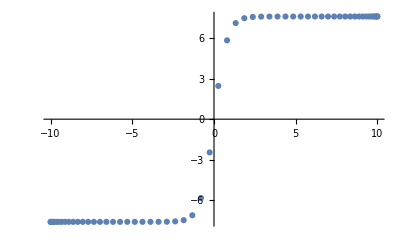

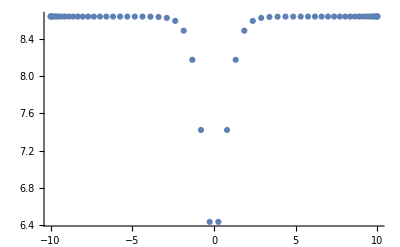

```mathematica
solq6=ArrayReshape[q6,{Nz,Nx}];
solq7=ArrayReshape[q7,{Nz,Nx}];
orderp=dz1⟦1⟧.solq6;
rho=-(dz1⟦1⟧.solq7);
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq6⟦i,j⟧},{i,Nz},{j,Nx}],1]]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq7⟦i,j⟧},{i,Nz},{j,Nx}],1]]
ListPlot[Table[{gridx⟦i⟧,orderp⟦i⟧},{i,Nx}],PlotRange->All]
ListPlot[Table[{gridx⟦i⟧,rho⟦i⟧},{i,Nx}],PlotRange->All]
```